## Packages import and definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/"<>#]&/@{"Chaometer.wl","QMB.wl"};
```

```mathematica
(* Import the superoperators *)
superoperators=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/regular/superoperators_"<>ToString[#]<>".csv"][[2;;]](*la primera fila tiene la info*)]&/@{1,2,3};
```

```mathematica
(* Load the same random states *)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3];
```

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,2.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(* Check de que un superoperador random sea el correcto comparando con la construccion de alguno  *)
t=RandomChoice[Range[0,50,0.1]];(* un tiempo aleatorio *)
i=1;(* estado inicial *)
MatrixForm[Round[#,10.^-7]]&/@{Chop@Superoperator[t,ψ0E[[i]](*número de estado aleatorio*),eigenvalsH,eigenvecsH,L],superoperators[[i,t/0.1+1]]}
Equal@@%
```

{(0.897112 | 0.147249-0.0018275 ⅈ | 0.147249+0.0018275 ⅈ | 0.0854016
0.172659+0.004082 ⅈ | 0.189497-0.147914 ⅈ | 0.0760936+0.0106024 ⅈ | -0.163527-0.0208422 ⅈ
0.172659-0.004082 ⅈ | 0.0760936-0.0106024 ⅈ | 0.189497+0.147914 ⅈ | -0.163527+0.0208422 ⅈ
0.102888 | -0.147249+0.0018275 ⅈ | -0.147249-0.0018275 ⅈ | 0.914598),(0.897112 | 0.147249-0.0018275 ⅈ | 0.147249+0.0018275 ⅈ | 0.0854016
0.172659+0.004082 ⅈ | 0.189497-0.147914 ⅈ | 0.0760936+0.0106024 ⅈ | -0.163527-0.0208422 ⅈ
0.172659-0.004082 ⅈ | 0.0760936-0.0106024 ⅈ | 0.189497+0.147914 ⅈ | -0.163527+0.0208422 ⅈ
0.102888 | -0.147249+0.0018275 ⅈ | -0.147249-0.0018275 ⅈ | 0.914598)}

True

```mathematica
(* Calcular las matrices de Choi *)
chois=Map[1/2*Reshuffle[#]&,superoperators,{2}];
```

```mathematica
(* Calcular los eigenvalores de las matrices de Chooi*)
eigenvaluesChoi=Chop[Map[Sort[Eigenvalues[#]]&,chois,{2}]];
```

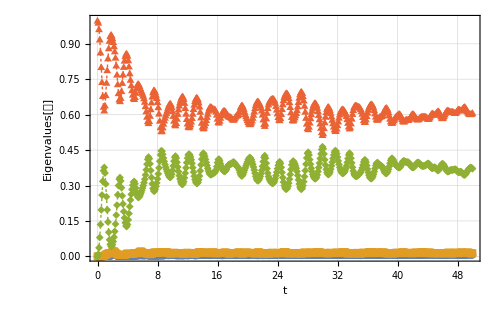

```mathematica
(* Graficar los eigenvalores de las matrices de Choi en el tiempo *)
ListPlot[Transpose[Transpose[{ConstantArray[#,4],eigenvaluesChoi[[1,#/0.1+1]]}]&/@Range[0,50,0.1]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashing[0.004],Thin],
PlotMarkers->{Automatic,8},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->26,FontFamily->"Arial"],
FrameLabel->{TraditionalForm[HoldForm[t]],"Eigenvalues[𝒟]"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]
```

```mathematica
ListPlot[{{1,1},{2,4},{3,9},{4,16}},PlotLabels->{Style["x",TraditionalForm,12],Style["y",TraditionalForm,12]},AxesLabel->{Style["X-axis","Times",12],Style["Y-axis","Times",12]},LabelStyle->Directive[Bold,12],PlotTheme->"Detailed"]
```

-Graphics-

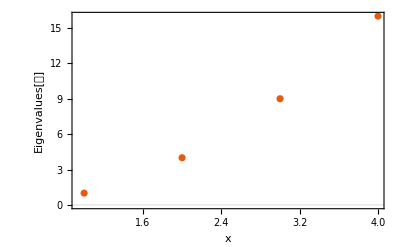

```mathematica
ListPlot[{{1,1},{2,4},{3,9},{4,16}},
Frame->True,
FrameLabel->{Text[Style[TraditionalForm[HoldForm[x]],14]],Text[Style[TraditionalForm[Eigenvalues[HoldForm[𝒟]]],14,FontFamily->]]},LabelStyle->Directive[Bold,FontFamily->"Times",14],PlotTheme->"Scientific"]
```

```mathematica
Text@@@{Style[HoldForm[x],TraditionalForm,14],Style[HoldForm[y],TraditionalForm,14]}
```

{Text[x,TraditionalForm,14],Text[y,TraditionalForm,14]}

```mathematica
HoldForm[x]
```

x

```mathematica
{Text[Style[TraditionalForm[HoldForm[x]],14]],Text[Style[TraditionalForm[HoldForm[y]],14]]}
```

{x,y}

```mathematica
TraditionalForm[Eigenvalues[HoldForm[𝒟]]]
```

Eigenvalues[𝒟]